```mathematica
SNNnetClassification[dropoutrate_,nhidden_,nlayers_,decoder_]:=NetChain[Join[Flatten@Table[{LinearLayer[nhidden],ElementwiseLayer["SELU"],DropoutLayer[dropoutrate,"Method"->"AlphaDropout"]},nlayers-1],{LinearLayer[],SoftmaxLayer[]}],"Output"->decoder];
```

## Examples

Don’t forget to curate the data first! Get rid of missing values. Normalize or standardize the data. This is very important for the model to work. At last divide the training set from the test set

This example is done on dermatological data

```mathematica
link="https://archive.ics.uci.edu/ml/machine-learning-databases/dermatology/dermatology.data";
dermaDatawMissing =ReplaceAll[Import[link, "CSV"], "?"->Missing[]];

dermaData=DeleteMissing[dermaDatawMissing,1,2];
dermaDatawRule=Table[Drop[dermaData⟦i⟧,-1]->Last@dermaData⟦i⟧,{i,1,Length@dermaData}];

dermatrain=RandomSample[dermaDatawRule,Round[0.9Length@dermaDatawRule]];dermatest=Complement[dermaDatawRule,dermatrain];

dermaext=FeatureExtraction[N@Keys@dermaDatawRule,"StandardizedVector"];

{dermatrainSNN,dermatestSNN}={dermaext[Keys@dermatrain]->Values[dermatrain],dermaext[Keys@dermatest]->Values[dermatest]};

dermatestSNN=Table[dermatestSNN[[1,i]]->dermatestSNN[[2,i]],{i,1,Length@dermatestSNN⟦1⟧}];
```

Create decoder, the classes to which the network will classify.

```mathematica
dermadec=NetDecoder[{"Class",Range[6]}];
```

Set up the hyperparameters. Dropout rate should be a decimal between 0 and 1, nlayers, i.e. number of layers, and nhidden, i.e. number of neurons in each layer is an integer variable, and is recommended the integer to be some power of 2.

```mathematica
dropoutrate=0.1; nhidden=32 ; nlayers=16;
```

```mathematica
dermaNet=SNNnetClassification[dropoutrate,nhidden,nlayers,dermadec]
```

NetChain[<>]

```mathematica
trainedNet=NetTrain[dermaNet,dermatrainSNN]
```

NetChain[<>]

```mathematica
dermacm=ClassifierMeasurements[trainedNet,dermatestSNN];
```

```mathematica
dermaAccuracy=dermacm["Accuracy"]
```

0.722222

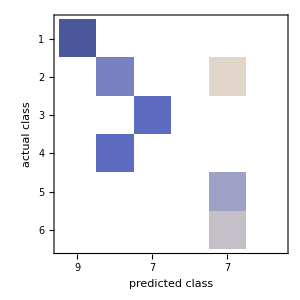

```mathematica
dermaconfusionmatrix=dermacm["ConfusionMatrixPlot"]
```

You can play with the hyperparameters, i.e. the number of layers, number of neurons and dropout rate to improve accuracy. The training time varies depending on the hyperparameters chosen. In the case below, the training time is larger that the case above

```mathematica
dropoutrate=0.01; nhidden=128 ; nlayers=8;
```

```mathematica
dermaNet=SNNnetClassification[dropoutrate,nhidden,nlayers,dermadec]
```

NetChain[<>]

Train the net with this new parameters. You can take advantage of the functionalities of the NetTrain[] function to have more insight about the training process.

```mathematica
trainedNet=NetTrain[dermaNet,dermatrainSNN,ValidationSet->Scaled[0.1]]
```

NetChain[<>]

```mathematica
dermacm=ClassifierMeasurements[trainedNet,dermatestSNN];
```

```mathematica
dermaAccuracy=dermacm["Accuracy"]
```

0.944444

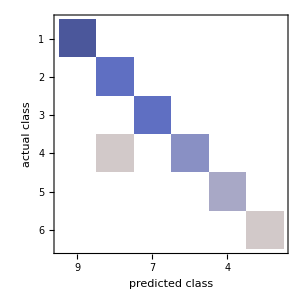

```mathematica
dermaconfusionmatrix=dermacm["ConfusionMatrixPlot"]
```